#### [Defs] Gaussian integrals

```mathematica
(*GaussianIntegral[M_]:=(2 ⅇ^((M⟦1,3⟧ M⟦2,1⟧^2-M⟦1,2⟧ M⟦2,1⟧ M⟦2,2⟧+M⟦1,1⟧ M⟦2,2⟧^2+M⟦1,2⟧^2 M⟦3,1⟧-4 M⟦1,1⟧ M⟦1,3⟧ M⟦3,1⟧)/(M⟦2,2⟧^2-4 M⟦1,3⟧ M⟦3,1⟧)) π)/(√(-4 M⟦1,3⟧+M⟦2,2⟧^2/M⟦3,1⟧) √(-M⟦3,1⟧));
ExpCoefficientsToMatrix[expr_,x_,p_]:=CoefficientList[Exponent[expr,ⅇ],{x,p},{3,3}];

(* Trunated Gaussian integrals
∫_(-Δ/2)^(Δ/2) ⅇ^(c x^2+b x +a)ⅆx*)
TruncatedGaussInt[v_,Δ_]:=(ⅇ^(v⟦1⟧-v⟦2⟧^2/(4 v⟦3⟧)) √π (-Erfi[(v⟦2⟧-Δ v⟦3⟧)/(2 √v⟦3⟧)]+Erfi[(v⟦2⟧+Δ v⟦3⟧)/(2 √v⟦3⟧)]))/(2 √v⟦3⟧);*)
GaussianIntegralMatrix[M_]:=lim_({m13,m31,m22}->{M[[1,3]],M[[3,1]],M[[2,2]]}) (2 ⅇ^((M⟦1,3⟧ M⟦2,1⟧^2-M⟦1,2⟧ M⟦2,1⟧ M⟦2,2⟧+M⟦1,1⟧ M⟦2,2⟧^2+M⟦1,2⟧^2 M⟦3,1⟧-4 M⟦1,1⟧ M⟦1,3⟧ M⟦3,1⟧)/(m22^2-4 m13 m31)) π)/(√(4 m13 m31-m22^2));
ExpCoefficientsToMatrix[expr_,x_,p_]:=CoefficientList[Exponent[expr,ⅇ],{x,p},{3,3}];

GaussIntR1[expr_,x_]:=Module[{a,b,c,d,expo},
expo = Exponent[expr,ⅇ];
d = Coefficient[expr,ⅇ, expo];
{c,b,a}=CoefficientList[expo,x,3];
lim_({aL,bL,cL}->{a,b,c}) ((d ⅇ^(-bL^2/(4 aL)+cL) √π)/(√-aL))
];

GaussIntR2[expr_,var1_,var2_]:=Module[{expo,coef,M,m11,m12,m13,m21,m22,m23,m31,m32,m33,m11L,m12L,m13L,m21L,m22L,m23L,m31L,m32L,m33L},
expo = Exponent[expr,ⅇ];
coef = Coefficient[expr,ⅇ, expo];
{{m11,m12,m13},{m21,m22,m23},{m31,m32,m33}}= CoefficientList[expo,{var1,var2},{3,3}];
lim_({m11L,m12L,m13L,m21L,m22L,m23L,m31L,m32L,m33L}->{m11,m12,m13,m21,m22,m23,m31,m32,m33}) (coef GaussianIntegralMatrix[{{m11L,m12L,m13L},{m21L,m22L,m23L},{m31L,m32L,m33L}}])
];

(* Trunated Gaussian integrals: ∫_(-Δ/2)^(Δ/2) ⅇ^(c x^2+b x +a)ⅆx*)
ClearAll[TruncatedGaussInt];
TruncatedGaussInt[expr_,x_,Δ_]:=Module[{a,b,c,d,expo,coef},
expo=Exponent[expr,ⅇ];
d = Coefficient[expr,ⅇ,expo];
{c,b,a}=CoefficientList[expo,{x},{3}];
Simplify[d(ⅇ^(-b^2/(4 a)+c) √π (-Erfi[(b-a Δ)/(2 √a)]+Erfi[(b+a Δ)/(2 √a)]))/(2 √a)]];

ResolvePD[n_,m_,A_,B_,expr_]:=lim_(A->0) ( D[(lim_(B->0) (D[(expr), {B,Max[m ,n]}])), {A,Min[m ,n ]}]);
ResolvePD2[a_]:=ResolvePD[a[[2,2,1]],a[[2,2,2]],A2,B2,ResolvePD[a[[2,1,1]],a[[2,1,2]],A1,B1,a[[1]]]];
```

#### [Defs] Useful function definitions

```mathematica
Efunc[μ_,Γ_,a_,x_]:=ⅇ^(-x^2/(2μ))∑_(s=-∞)^∞ DiracDelta[x-(s+a)Γ];
Efunct[μ_,Γ_,a_,x_]:=ⅇ^(-x^2/(2μ))∑_(s=-∞)^∞ ⅇ^(2π ⅈ a s)DiracDelta[x-s Γ];
Gauss[v_,x_]:=1/(√(2π v))ⅇ^(-x^2/(2v));
Θ[a_,b_,z_,τ_]:=Exp[π ⅈ τ a^2 + 2π ⅈ a (z+b)]EllipticTheta[3,π(z+ τ a + b), Exp[π ⅈ τ]];
Θs[a_,b_,z_,τ_,s_]:=Exp[π ⅈ τ (s+a)^2 + 2π ⅈ (s+a) (z+b)];
αd[d_]:=√((2π)/d);
Λ[vq_,vp_]:=1-4vq vp;
norm[vq_,vp_,Γ_,j_,d_]:=Re[Θ[j/d,0,0,(2ⅈ Γ^2)/π  vp^2/Λ[vq,vp]]Θ[0,0,0, (2π ⅈ)/Γ^2 vq^2/Λ[vq,vp]]+Θ[j/d+1/2,0,0,(2ⅈ Γ^2)/π  vp^2/Λ[vq,vp]]Θ[0,1/2,0, (2π ⅈ)/Γ^2 vq^2/Λ[vq,vp]]];

EconvG[μ_,Γ_,a_,v_,x_]:= Gauss[v,x]Θ[a,0,(Γ x)/(2 π ⅈ v),(ⅈ Γ^2 (1+v/μ))/(2 π v)];

EtconvG[μ_,Γ_,a_,v_,x_]:= Gauss[v,x]Θ[0,a,(ⅈ Γ x)/(2 π v),(ⅈ Γ^2)/(2 π v)];
EconvGs[μ_,Γ_,a_,v_,x_,s_]:= Gauss[v,x]Θs[a,0,(Γ x)/(2 π ⅈ v),(ⅈ Γ^2 (1+v/μ))/(2 π v),s];

EtconvGs[μ_,Γ_,a_,v_,x_,s_]:= Gauss[v,x]Θs[0,a,(ⅈ Γ x)/(2 π v),(ⅈ Γ^2)/(2 π v),s];
(*Note : σ^2 = 0.5 means 0 squeezing so 0 < σ^2 (variance) < 0.5 *)

ProductTerm[q_,p_,d_,i_,j_,vq_,vp_,Γ_,parity_]:=Chop[EconvG[Λ[vq,vp]/(4vp),Γ,(i+j)/(2d)+parity/2,vq,q]]Chop[EtconvG[Λ[vq,vp]/(4vq),(π Λ[vq,vp])/Γ,(i-j)/(2d)+parity/2,vp,p]];
Wigner[q_,p_,d_,i_,j_,vq_,vp_,Γ_]:=1/(√(norm[vq,vp,Γ,i,d]norm[vq,vp,Γ,j,d]))Chop[ProductTerm[q,p,d,i,j,vq,vp,Γ,0]+ProductTerm[q,p,d,i,j,vq,vp,Γ,1]];
(* Wigner for vacuum *)
Vacner[q_,p_]:= Gauss[1/2, q]Gauss[1/2, p];
(* Wigner for Fock states *)
Fockner[q_,p_,n_]:=(-1)^n Gauss[1/2, q]Gauss[1/2, p]LaguerreL[n,2(q^2+p^2)];

(* Beamsplitter Bololiubov B = ({{t}, {ⅈr}}{{ⅈr}, {t}}) with t = √η *)
 (* The quadratures will mix {q1,p1,q2,p2} according to ({{t}, {0}, {0}, {r}}{{0}, {t}, {-r}, {0}}{{0}, {r}, {t}, {0}}{{-r}, {0}, {0}, {t}})  *)

B[t_,r_]:= {{t,0,0,-r},{0,t,r,0},{0,-r,t,0},{r,0,0,t}};
{Q1,P1,Q2,P2}=B[t,r].{q1,p1,q2,p2};
```

#### [Calc] W_gkp(q1, p1) W_0(q2, p2) → (EcovG[Q1]Gauss[v21/2, P2])(EtconvG[P1] Gauss[v2=1/2, Q2])

```mathematica
EconvGs[μ,Γ,a,v1,Q1,s]Gauss[v2, P2]
```

(ⅇ^(-(-p2 r+q1 t)^2/(2 v1)-(q1 r+p2 t)^2/(2 v2)+((a+s) (-p2 r+q1 t) Γ)/v1-((a+s)^2 Γ^2 (1+v1/μ))/(2 v1)))/(2 π √v1 √v2)

```mathematica
EtconvGs[μ,Γ,a,v1,P1,s]Gauss[v2, Q2]
```

(ⅇ^(-(q2 r+p1 t)^2/(2 v1)-(-p1 r+q2 t)^2/(2 v2)-(s^2 Γ^2)/(2 v1)+2 ⅈ π s (a+(ⅈ (q2 r+p1 t) Γ)/(2 π v1))))/(2 π √v1 √v2)

#### [Calc] Tracing out mode 2 - vacuum loss

```mathematica
(* For EconvG term *)
ClearAll[a,b,c];
{cg,bg,ag}=CoefficientList[-(-p2 r+q1 t)^2/(2 v1)-(q1 r+p2 t)^2/(2 v2)+((a+s) (-p2 r+q1 t) Γ)/v1-((a+s)^2 Γ^2 (1+v1/μ))/(2 v1),{p2}];
(√π)/(2 π √v1 √v2)(ⅇ^(bg^2/(4(-ag))+cg))/(√-ag)(* Gaussian integral over momentum p2 *)
```

(ⅇ^(-(q1^2 t^2)/(2 v1)-(q1^2 r^2)/(2 v2)+(q1 (a+s) t Γ)/v1+((q1 r t)/v1-(q1 r t)/v2-(r (a+s) Γ)/v1)^2/(4 (r^2/(2 v1)+t^2/(2 v2)))-((a+s)^2 Γ^2 (1+v1/μ))/(2 v1)))/(2 √π √v1 √(r^2/(2 v1)+t^2/(2 v2)) √v2)

```mathematica
Simplify[CoefficientList[Exponent[%29,ⅇ]/.(s+a)->s',s'],{r^2+t^2==1,t^2 v1+r^2 v2==v',Γ==Γ'/t,μ==μ'/t^2}]
```

{-q1^2/(2 v'),(q1 Γ')/v',-(Γ^2 (v'+μ'))/(2 μ v')}

```mathematica
(* For EtconvG term *)
ClearAll[a,b,c];
{cg,bg,ag}=CoefficientList[-(q2 r+p1 t)^2/(2 v1)-(-p1 r+q2 t)^2/(2 v2)-(s^2 Γ^2)/(2 v1)+2 ⅈ π s (a+(ⅈ (q2 r+p1 t) Γ)/(2 π v1)),{q2}];
(√π)/(2 π √v1 √v2)(ⅇ^(bg^2/(4(-ag))+cg))/(√-ag)(* Gaussian integral over position q2 *)
```

(ⅇ^(2 ⅈ a π s-(p1^2 t^2)/(2 v1)-(p1^2 r^2)/(2 v2)-(p1 s t Γ)/v1-(s^2 Γ^2)/(2 v1)+(-(p1 r t)/v1+(p1 r t)/v2-(r s Γ)/v1)^2/(4 (r^2/(2 v1)+t^2/(2 v2)))))/(2 √π √v1 √(r^2/(2 v1)+t^2/(2 v2)) √v2)

```mathematica
Simplify[CoefficientList[Exponent[%70,ⅇ],s],{r^2+t^2==1,t^2 v1+r^2 v2==v',Γ==Γ'/t,μ==μ'/t^2}]
```

{-p1^2/(2 v'),2 ⅈ a π-(p1 Γ')/v',-(Γ')^2/(2 v')}

The result is μ → μt^2,   Γ→ Γt,     a→a,  and v1→t^2 v1+r^2 v2 , when mode 2 is traced out

#### [Rslt] Vacuum loss

```mathematica
ProductTermLoss[t_,q_,p_,d_,i_,j_,v1_,Γ_,parity_]:=Chop[EconvG[Λ[v1,v1]/(4v1)t^2,Γ t,(i+j)/(2d)+parity/2,t^2 v1+(1-t^2)1/2,q]]Chop[EtconvG[Λ[v1,v1]/(4v1)t^2,(π Λ[v1,v1])/Γ t,(i-j)/(2d)+parity/2,t^2 v1+(1-t^2)1/2,p]];
WignerLoss[t_,q_,p_,d_,i_,j_,v1_,Γ_]:=1/(√(norm[v1,v1,Γ,i,d]norm[v1,v1,Γ,j,d]))Chop[∑_(parity=0)^1 ProductTermLoss[t,q,p,d,i,j,v1,Γ,parity]];
```

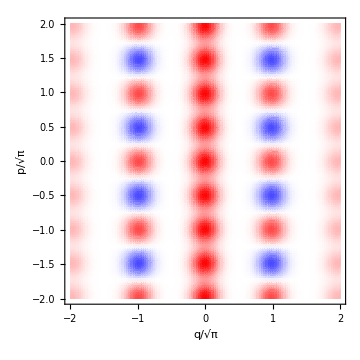

```mathematica
ClearAll[mat,limits,range,v1,t,r,d,Γ];
limits=2;
range=60;
v1= 0.05;
d=2;
Γ =αd[d] d √Λ[v1,v1];
n=4;
t=√0.98;
r=√(1-t^2);

(* List Desnity Plot - fast *) 
Quiet[
mat=Table[Re[Chop[WignerLoss[t,√π((x-1)(limits/range)-limits),√π((p-1)(limits/range)-limits),d,0,0,v1,Γ ]]],{p,1,2 range +1},{x,1,2 range +1}];
];
mat=mat/(Abs[Total[mat,2]](limits/range)^2);
plot=ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,FrameLabel->{"q/√π","p/√π"}]
```

#### [Calc] Wigner after beamsplitting. Crucial choice: vq=vp==v

```mathematica
ClearAll[Q1,P1,Q2,P2,vq,vp];
summant=Simplify[EconvGs[μ,Γ,a,vq,Q1,s]Gauss[1/2, P2]EtconvGs[μ̃,Γ̃,ã,vp,P1,u]Gauss[1/2, Q2],{r^2+t^2==1}]
```

(ⅇ^(1/2 (-2 P2^2-2 Q2^2-P1^2/vp-Q1^2/vq+(2 Q1 (a+s) Γ)/vq-((a+s)^2 Γ^2 (vq+μ))/(vq μ)+4 ⅈ π u ã-(2 P1 u Γ̃)/vp-(u^2 (Γ̃)^2)/vp)))/(2 π^2 √vp √vq)

```mathematica
ExpoSummant=Distribute[Exponent[summant,ⅇ]]
```

-P2^2-Q2^2-P1^2/(2 vp)-Q1^2/(2 vq)+(Q1 (a+s) Γ)/vq-((a+s)^2 Γ^2 (vq+μ))/(2 vq μ)+2 ⅈ π u ã-(P1 u Γ̃)/vp-(u^2 (Γ̃)^2)/(2 vp)

```mathematica
CoefficientList[ExpoSummant,{Q1,P1,Q2,P2}]//MatrixForm
```

((-((a+s)^2 Γ^2 (vq+μ))/(2 vq μ)+2 ⅈ π u ã-(u^2 (Γ̃)^2)/(2 vp) | 0 | -1
0 | 0 | 0
-1 | 0 | 0) | (-(u Γ̃)/vp | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (-1/(2 vp) | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(((a+s) Γ)/vq | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)
(-1/(2 vq) | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0) | (0 | 0 | 0
0 | 0 | 0
0 | 0 | 0))

```mathematica
expr1=-P2^2-Q2^2-P1^2/(2 vp)-Q1^2/(2 vq)+(Q1 (a+s) Γ)/vq-(P1 u Γ̃)/vp;
Extra1=(1/(2 π^2 √vp √vq))Exp[-((a+s)^2 Γ^2 (vq+μ))/(2 vq μ)+2 ⅈ π u ã-(u^2 (Γ̃)^2)/(2 vp)];
```

#### [Calc] Heralding on Fock

```mathematica
(*  Subscript[L, n](-Subscript[z, 1] Subscript[z, 2])=1/(n!)∂_{α,n} ∂_{β,n} ⅇ^(α β+α Subscript[z, 1]+β Subscript[z, 2])
Subscript[W, n](q,p)=(-1)^n/π ⅇ^(-q^2-p^2)Subscript[L, n](2(q^2+p^2))
Overlap integral = 2π∫ⅆq∫ⅆp W Subscript[W, n]
*)
```

```mathematica
Extra1
```

(ⅇ^(-((a+s)^2 Γ^2 (vq+μ))/(2 vq μ)+2 ⅈ π u ã-(u^2 (Γ̃)^2)/(2 vp)))/(2 π^2 √vp √vq)

```mathematica
expr2=expr1-q2^2-p2^2+√2 ⅈ(β+α)q2-√2(β-α)p2;
Extra2=Extra1(2π(* from overlap integral *)(-1)^n)/(n!π)Exp[β α];
{Q1,P1,Q2,P2}=B[t,r].{q1,p1,q2,p2};
expr2;
expr3=GaussianIntegral[CoefficientList[expr2,{q2,p2},{3,3}]];
Final=Extra2 expr3 ;
expr4=Exponent[Final,ⅇ];
Extra4 = Coefficient[Final,ⅇ,expr4];
vq=vp=v;
{cα0,cα1}=FullSimplify[CoefficientList[expr4,{α}],r^2+t^2==1];
```

```mathematica
Extra4
expr4
```

(-1)^n/(π (1+t^2+r^2/(2 v)) v n!)

α β-((a+s)^2 Γ^2 (v+μ))/(2 v μ)+2 ⅈ π u ã-(u^2 (Γ̃)^2)/(2 v)-1/(4 (-1-t^2-r^2/(2 v))^2)((-1-t^2-r^2/(2 v)) (-2 q1 r t+(q1 r t)/v-√2 (-α+β)-(r (a+s) Γ)/v)^2+(-1-t^2-r^2/(2 v)) (2 p1 r t-(p1 r t)/v+ⅈ √2 (α+β)-(r u Γ̃)/v)^2-4 (-1-t^2-r^2/(2 v))^2 (-p1^2 r^2-q1^2 r^2-(p1^2 t^2)/(2 v)-(q1^2 t^2)/(2 v)+(q1 (a+s) t Γ)/v-(p1 t u Γ̃)/v))

```mathematica
S1=Exp[(+q1^2+p1^2)((-1-2 v+t^2 (-1+2 v))/(2 (v+t^2 v+r^2/2)))]Exp[((q1 (2 t)/(√(1+t^2))+r(β-α)/(√(2(1+t^2))))^2)/(2 (v+t^2 v+r^2/2))]Exp[((p1 (2 t)/(√(1+t^2))+ⅈ r(β+α)/(√(2(1+t^2))))^2)/(2 (v+t^2 v+r^2/2))];(* One gaussian part is already absorbed into the EcovG and EtcovG functions *)
S2=Exp[((2v-1)/(v+t^2 v+r^2/2))r t (q1 ((β-α)/(√2))+ⅈ p1 ((β+α)/(√2)))];
S3 = Exp[α β (1-((2 v)/(v+t^2 v+r^2/2)))];
S4=EconvG[Λ[v,v]/(4v)(1+t^2),Γ √(1+t^2),(i+j)/(2d)+parity/2,v+t^2 v+r^2/2,q1 (2 t)/(√(1+t^2))+r(β-α)/(√(2(1+t^2)))];
S5=EtconvG[Λ[v,v]/(4v)(1+t^2),(π Λ[v,v])/Γ √(1+t^2),(i-j)/(2d)+parity/2,v+t^2 v+r^2/2,p1 (2 t)/(√(1+t^2))+ⅈ r(β+α)/(√(2(1+t^2)))];
```

```mathematica
Extra5=(*1/(√(norm[vq,vp,Γ,i,d]norm[vq,vp,Γ,j,d]))*)(-1)^n/(n!)2(*∂_{α,n} ∂_{β,n}*);
expr5 = S1 S2 S3 S4 S5;
```

#### Trying to sum over s and u before taking differentiating w . r . t . α and β

```mathematica
Gammacflist=Simplify[CoefficientList[expr4,{Γ,Γ̃}],{r^2+t^2==1}];
MatrixForm[Gammacflist]
```

((-p1^2-q1^2-2 p1^2 v-2 q1^2 v+α β-2 v α β+√2 r t (-1+2 v) (q1 (-α+β)+ⅈ p1 (α+β))+2 ⅈ π u ã+4 ⅈ π u v ã+t^2 (-1+2 v) (p1^2+q1^2+α β+2 ⅈ π u ã))/(r^2+2 (1+t^2) v) | -(u (4 p1 t+ⅈ √2 r (α+β)))/(r^2+2 (1+t^2) v) | -((1+t^2) u^2)/(r^2+2 (1+t^2) v)
((a+s) (4 q1 t+√2 r (-α+β)))/(r^2+2 (1+t^2) v) | 0 | 0
-((a+s)^2 (1+2 v+2 μ+t^2 (-1+2 v+2 μ)))/(2 (r^2+2 (1+t^2) v) μ) | 0 | 0)

```mathematica
(* Γ^2 term *)
Collect[Simplify[Expand[Gammacflist[[3,1]]],{r^2+t^2==1}],μ]
```

-((a+s)^2 (2+2 t^2))/(2 (r^2+2 (1+t^2) v))-((a+s)^2 (1-t^2+2 v+2 t^2 v))/(2 (r^2+2 (1+t^2) v) μ)

```mathematica
(*Constant term*)
Collect[Simplify[Expand[Gammacflist[[1,1]]],{r^2==1-t^2}],{p1,q1}]
```

(p1^2 (-1-2 v+t^2 (-1+2 v)))/(r^2+2 (1+t^2) v)+(q1^2 (-1-2 v+t^2 (-1+2 v)))/(r^2+2 (1+t^2) v)+(√2 q1 r t (-1+2 v) (-α+β))/(r^2+2 (1+t^2) v)+(ⅈ √2 p1 r t (-1+2 v) (α+β))/(r^2+2 (1+t^2) v)+(α β-2 v α β+t^2 (-1+2 v) α β+2 ⅈ π u ã+4 ⅈ π u v ã+2 ⅈ π t^2 u (-1+2 v) ã)/(r^2+2 (1+t^2) v)

#### Taking differentiation before summing over s and u

```mathematica
(* Note: There is a ⅇ^(α β) in the Extra2 term and so multiplying it in the Final terms was important before calling CoefficientList for α *)lim_(α->0) D[(ⅇ^(c0+c1 α)), {α,n}]
```

c1^n ⅇ^c0

```mathematica
ClearAll[x0,x1,y0,y1];
{xβ0,xβ1}=CoefficientList[cα1,β];
{yβ0,yβ1}=CoefficientList[cα0,β];
```

```mathematica
Assuming[{n∈Integers,n>0},FunctionExpand[lim_(β->0) D[(x1^n(x0/x1+ β)^n ⅇ^y0 ⅇ^(y1 β)), {β,n}]]]
```

ⅇ^y0 x1^n Gamma[1+n] LaguerreL[n,-(x0 y1)/x1]

```mathematica
AfterPD=FullSimplify[Extra4 ⅇ^yβ0 xβ1^n  LaguerreL[n,-(xβ0 yβ1)/xβ1] n!,r^2+t^2==1]
```

```mathematica
SUthTerm[s_,u_]:=1/(π+2 π v+π t^2 (-1+2 v))2 (-1)^n ⅇ^((2 (p1^2+q1^2) (-1-2 v+t^2 (-1+2 v))+8 q1 (a+s) t Γ-2 (a+s)^2 (1+t^2) Γ^2-((a+s)^2 (1+2 v+t^2 (-1+2 v)) Γ^2)/μ+4 ⅈ π u (1+2 v+t^2 (-1+2 v)) ã-2 u Γ̃ (4 p1 t+(1+t^2) u Γ̃))/(2 (r^2+2 (1+t^2) v))) (((-1+t^2) (-1+2 v))/(r^2+2 (1+t^2) v))^n LaguerreL[n,-((2 (t^2 (p1-2 p1 v)^2+(q1 t (-1+2 v)+(a+s) Γ)^2+u Γ̃ (2 p1 t (1-2 v)+u Γ̃)))/(-1+4 v^2+(t-2 t v)^2))];
```

```mathematica
FunctionExpand[∑_(s=-∞)^∞ ∑_(u=-∞)^∞ SUthTerm[s,u]]
```

∑_(s=-∞)^∞ ∑_(u=-∞)^∞ 1/(π+2 π v+π t^2 (-1+2 v))2 (-1)^n ⅇ^((2 (p1^2+q1^2) (-1-2 v+t^2 (-1+2 v))+8 q1 (a+s) t Γ-2 (a+s)^2 (1+t^2) Γ^2-((a+s)^2 (1+2 v+t^2 (-1+2 v)) Γ^2)/μ+4 ⅈ π u (1+2 v+t^2 (-1+2 v)) ã-2 u Γ̃ (4 p1 t+(1+t^2) u Γ̃))/(2 (r^2+2 (1+t^2) v))) (((-1+t^2) (-1+2 v))/(r^2+2 (1+t^2) v))^n LaguerreL[n,-(2 (t^2 (p1-2 p1 v)^2+(q1 t (-1+2 v)+(a+s) Γ)^2+u Γ̃ (2 p1 t (1-2 v)+u Γ̃)))/(-1+4 v^2+(t-2 t v)^2)]

```mathematica
(* summing over LauguerreL and Gaussian is a headache -- I don't know the function whose series expansion gives this one. *)
```

```mathematica
Gammacflist=Simplify[CoefficientList[expr5,{Γ,Γ̃}],{r^2+t^2==1}];
MatrixForm[Gammacflist]
```

(((p1^2+q1^2) (-1-2 v+t^2 (-1+2 v))+2 ⅈ π u (1+2 v+t^2 (-1+2 v)) ã)/(r^2+2 (1+t^2) v) | -(4 p1 t u)/(r^2+2 (1+t^2) v) | -((1+t^2) u^2)/(r^2+2 (1+t^2) v)
(4 q1 (a+s) t)/(r^2+2 (1+t^2) v) | 0 | 0
-((a+s)^2 (1+2 v+2 μ+t^2 (-1+2 v+2 μ)))/(2 (r^2+2 (1+t^2) v) μ) | 0 | 0)

```mathematica
(* Subscript[Γ, q]^2 term *)
expr6=Collect[Simplify[Expand[Gammacflist[[3,1]]],{r^2+t^2==1}],μ]
```

-((a+s)^2 (2+2 t^2))/(2 (r^2+2 (1+t^2) v))-((a+s)^2 (1-t^2+2 v+2 t^2 v))/(2 (r^2+2 (1+t^2) v) μ)

```mathematica
(2+2 t^2)/(2 (r^2+2 (1+t^2) v))(1+(r^2+2 (1+t^2) v)/((2+2 t^2) μ))
```

```mathematica
Collect[Simplify[Expand[expr6],t^2+r^2==1],μq]
```

(1-t^2+2 v1+2 t^2 v1)/(r^2+2 (1+t^2) v1)+((2+2 t^2) μq)/(r^2+2 (1+t^2) v1)

```mathematica
(* Constant term *)
expr7=Collect[Simplify[Expand[Gammacflist[[1,1]]],{r^2+t^2==1}],q1^2+p1^2]
```

((p1^2+q1^2) (-1-2 v+t^2 (-1+2 v)))/(r^2+2 (1+t^2) v)+(2 ⅈ π u (1+2 v+t^2 (-1+2 v)) ã)/(r^2+2 (1+t^2) v)

```mathematica
(* Substitutions *)
{Γ->Γ √(1+t^2),μ-> μ(1+t^2),v-> v+t^2 v+r^2/2}
```

```mathematica
ProductTermNew[n_,t_,r_,q1_,p1_,d_,i_,j_,v_,Γ_,parity_]:=(-1)^n((-v+t^2 v+r^2/2)^n)/((v+t^2 v+r^2/2)^n)2 ⅇ^(-(q1^2+p1^2))((1/2-(-v+t^2 v+r^2/2))/(v+t^2 v+r^2/2))Chop[EconvG[Λ[v,v]/(4v)(1+t^2),Γ √(1+t^2),(i+j)/(2d)+parity/2,v+t^2 v+r^2/2,q1 ((2 t)/(√(1+t^2)))]]Chop[EtconvG[Λ[v,v]/(4v)(1+t^2),(π Λ[v,v])/Γ √(1+t^2),(i-j)/(2d)+parity/2,v+t^2 v+r^2/2,p1 ((2 t)/(√(1+t^2)))]];
WunPS[n_,t_,r_,q1_,p1_,d_,i_,j_,v_,Γ_]:=1/(√(norm[v1,v1,Γ,i,d]norm[v,v,Γ,j,d]))Chop[∑_(parity=0)^1 ProductTermNew[n,t,r,q1,p1,d,i,j,v,Γ,parity]];
```

```mathematica
ClearAll[mat,limits,range,v,t,r,d,Γ];
limits=2;
range=60;
v= 0.05;
d=2;
Γ =αd[d] d √Λ[v,v];
n=4;
t=√0.99;
r=√(1-t^2);

(* List Desnity Plot - fast *) 
Quiet[
mat=Table[Re[Chop[WunPS[n,t,r,√π((x-1)(limits/range)-limits),√π((p-1)(limits/range)-limits),d,0,0,v,Γ]]],{p,1,2 range +1},{x,1,2 range +1}];
];
mat=mat/(Abs[Total[mat,2]](limits/range)^2);
```

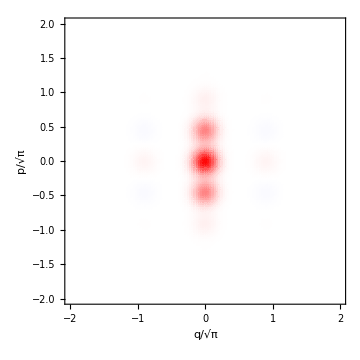

```mathematica
plot=ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,FrameLabel->{"q/√π","p/√π"}]
```

```mathematica
WunPS[2,√0.98,√0.02,0,0,2,0,0,v,αd[d] d √Λ[v,v]]
```

0.000453721

```mathematica
lim_(a->0) D[ⅇ^(a b+a x+b y),{a,n}]
```

ⅇ^(b y) (b+x)^n

```mathematica
D[ⅇ^(b y) (b+x)^n,{b,n}]/.b->0
```

n! [1+n]

```mathematica
FunctionExpand[n! [1+n]]
```

Gamma[1+n] LaguerreL[n,-x y]-(x y (-x y)^n HypergeometricPFQ[{1,1},{2+n,2+n},-x y] Sin[n π])/((1+n)^2 π)

```mathematica
f=2 x;
g=5 x^2;
D[f g,x]
```

30 x^2

```mathematica
D[((x0+x1 β)^n ⅇ^(y1 β)), {β,n}]
```

n! [n]

```mathematica
D[(x0+x1 β)^n ⅇ^(y1 β),{β,n}]
```

n! [n]